# Analitična geometrija

# Krivulje v ravnini

Za risanje ravninskih krivulj uporabljamo naslednje ukaze:

Krivuljo podano v eksplicitni obliki narišemo z ukazom Plot.
Krivuljo podano v implicitni obliki narišemo z ukazom ContourPlot.
Krivuljo podano v parametrični obliki narišemo z ukazom ParametricPlot.

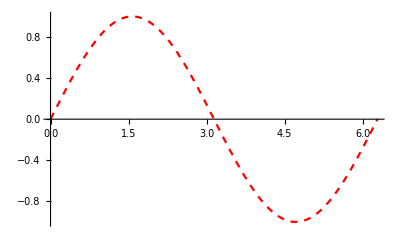

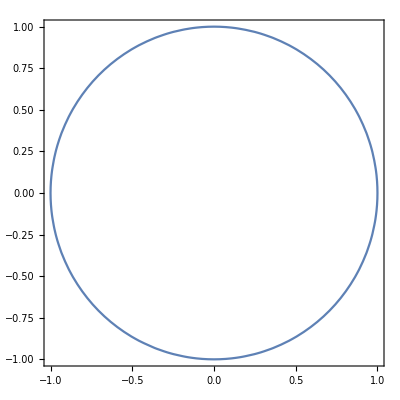

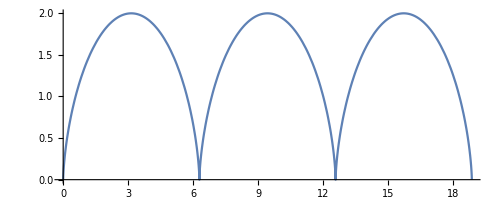

```mathematica
(* Primeri: Velike začetnice ukazov, ukaz[], argumente ločimo z vejico, seznam {}, navadni je pa prednost, zaženemo SHIFT+ENTER 
; potem ne vidimo  *)
slika1 = Plot[Sin[x],{x,0,2Pi},PlotStyle->{Red,Dashed}] 
slika2= ContourPlot[x^2+y^2==1,{x,-1,1},{y,-1,1}]
ParametricPlot[{t-Sin[t],1-Cos[t]},{t,0,6Pi}]
```

```mathematica
?Plot
?ContourPlot
?ParametricPlot
```

Slika v Mathematici je objekt, ki ga lahko poimenujemo.
Obliko krivulje (barva, debelina ...) opišemo z opcijo PlotStyle.

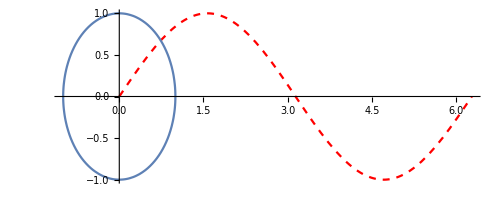

```mathematica
Show[slika1, slika2, PlotRange->All, AspectRatio->Automatic(*enake enote*) ]
```

```mathematica
?PlotStyle
```

1.a) Narišite krivuljo, dano v parametrični obliki: x(t)=4cos(t^1.5), y(t)=sin(t).
         Krivulja naj bo modre barve. Slika naj ima ime slika1.

```mathematica
?ParametricPlot
```

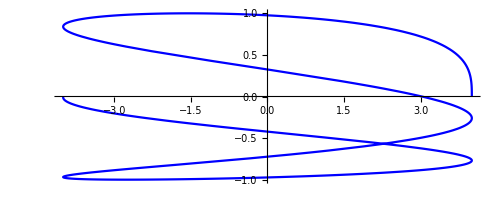

```mathematica
slika1=ParametricPlot[{4*Cos[t^1.5], Sin[t]}, {t,0,2Pi}, PlotStyle->Blue]
```

1.b) Narišite krivuljo y(x)=x/4 sin(5x).
         Krivulja naj bo rdeče barve. Slika naj ima ime slika2.

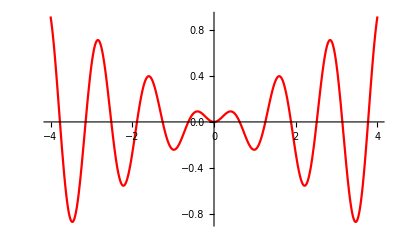

```mathematica
slika2 = Plot[x/4 Sin[5x], {x,-4,4}, PlotStyle -> Red]
```

1.c) S pomočjo ukaza Show narišite obe krivulji na isto sliko.

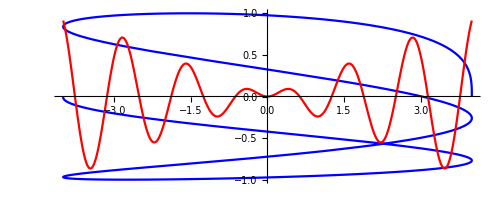

```mathematica
Show[slika1,slika2]
```

1.d) Epicikloida je krivulja, ki jo opiše točka krožnice, ki se kotali po drugi krožnici zunaj nje.
         Njena parametrična enačba je 
         x = (R+r)cos(φ) - r cos((R+r)/rφ),
         y = (R+r)sin(φ) - r sin((R+r)/rφ),
         kjer je:
         R polmer mirujoče krožnice,
         r polmer kotaleče krožnice in
         φ polarni kot.
         
         Narišite epicikloido s pomočjo ukaza ParametricPlot!
         Razmerje polmerov R/r naj bo celo število.
         Opomba: Merilo v koordinatah x in y se uravnava z opcijo AspectRatio (glejte "Help").

20

2

{22 Cos[t]-2 Cos[11 t],22 Sin[t]-2 Sin[11 t]}

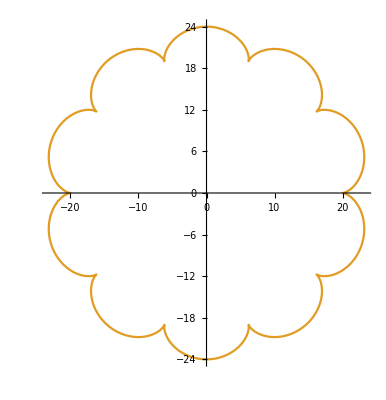

```mathematica
R=20
r=2
epi={(R+r)Cos[t] - r Cos[(R+r)/r t], (R+r)Sin[t] - r Sin [(R+r)/r t]}
ParametricPlot[epi,{t,0,2Pi}]
(*Razmerje med radiji == število hribčkov, Če ni celo število potem ne pridemo skupaj*)
```

```mathematica
?AspectRatio
```

```mathematica
epi={(R+r) Cos[t] - r Cos[(R+r)/r t], (R+r) Sin[t] - r Sin[(R+r)/r t]}
```

# Krivulje v prostoru

Za risanje (parametrično podanih) krivulj v prostoru uporabljamo ukaz ParametricPlot3D.

```mathematica
?ParametricPlot3D
```

3. a) Z zeleno barvo narišite krivuljo (t cos(t), t sin(t), t). (Pomoč: ukaz ParametricPlot3D.)
     b) Izračunajte enačbo tangente na to krivuljo v točki ((π √2)/8,(π √2)/8,π/4).
     c) Tangento tudi narišite z rdečo barvo in prikažite oba objekta v isti sliki.
   
     Rezultat (enačba tangente): {π/(4 √2)+(1/(√2)-π/(4 √2)) t,π/(4 √2)+(1/(√2)+π/(4 √2)) t,π/4+t}

```mathematica
r={t Cos[t], t Sin[t], t}
slikaKrivulje = ParametricPlot3D[r,{t, 0,2Pi}, PlotStyle->Green];
e=D[r,t] 
(* Iz tretje komponente je očitno da je točki pripadajoči t enak Pi/4
Točko dobimo tako da v r vstavimo Pi/4
Tangento dobimo tako da v e vstavimo pi/4
s označimo parameter, ker smo t že ponucal.
*)

  
tengenta= (r + s* e)/. t-> Pi/4 
(*ali po korakih*)
tocka=r/.t-> Pi/4
smerniVektor =e/.t->Pi/4
tangenta = tocka + smerniVektor*t
slikaTangente = ParametricPlot3D[tangenta,{t,-2,2},PlotStyle->Red];
Show[slikaKrivulje,slikaTangente]
```

{t Cos[t],t Sin[t],t}

{Cos[t]-t Sin[t],t Cos[t]+Sin[t],1}

{π/(4 √2)+(1/(√2)-π/(4 √2)) s,π/(4 √2)+(1/(√2)+π/(4 √2)) s,π/4+s}

{π/(4 √2),π/(4 √2),π/4}

{1/(√2)-π/(4 √2),1/(√2)+π/(4 √2),1}

{π/(4 √2)+(1/(√2)-π/(4 √2)) t,π/(4 √2)+(1/(√2)+π/(4 √2)) t,π/4+t}

-Graphics3D-

4. Izračunajte dolžino krivulje iz 3. naloge od točke t=0 do točke t=(7π)/11.
     
     Rezultat: 3.59373

```mathematica
r={t Cos[t], t Sin[t], t}
e=D[r,t] 
Integrate[Norm[e],{t,0,7 Pi/11}] //N
(*ali Numerične metode, hitrejša*)
NIntegrate[Norm[e],{t,0,7 Pi/11}]
```

{t Cos[t],t Sin[t],t}

{Cos[t]-t Sin[t],t Cos[t]+Sin[t],1}

3.59373

3.59373

# Ploskve - za DN reši kako nalogo iz kolokvijev z računalnikom

Osnovna ukaza za risanje ploskev v prostoru sta:
                                            če je enačba ploskve ...
Plot3D                                       eksplicitna           z=f(x,y)
ParametricPlot3D         parametrična       r⃗={x(u,v),y(u,v),z(u,v)}

```mathematica
?Plot3D
?ParametricPlot3D
```

1. a) Narišite stožec z(x,y)=√(x^2+y^2) s pomočjo ukaza Plot3D.
     b) Lepša slika stožca nastane z ukazom ParametricPlot3D, če izberemo za parametra polarne koordinate, zato uporabite še omenjeni ukaz.
          Kako je potrebno spremeniti enačbo, da bo stožec bolj zaprt (odprt)?

```mathematica
Plot3D[Sqrt[x^2 +y^2],{x,-2,2},{y,-2,2}]
ParametricPlot3D[{r Cos[t],r Sin[t],r},{t,0,2Pi},{r,0,1}]
```

-Graphics3D-

-Graphics3D-

2. Narišite valj  x^2+y^2=1, -3<z<3  z ukazom ParametricPlot3D.

```mathematica
ParametricPlot3D[{1  Cos[t],1 Sin[t],z},{t,0,2Pi},{z,-3,3}]
Plot3D[] (*se ne da, ker se ne da izrazit z(x,y)*)
```

-Graphics3D-

Primeri osnovnih geometrijskih oblik:
ravnina, paraboloid, valj, sfera

```mathematica
ravnina=Plot3D[4x+7y,{x,-3,3},{y,-3,3}]
paraboloid=Plot3D[x^2+y^2,{x,-3,3},{y,-3,3}]
paraboloid=ParametricPlot3D[{ρ Cos[φ],ρ Sin  [φ],ρ^2},{φ,0,2π},{ρ,0,3}]
valj=ParametricPlot3D[{2 Cos[φ],2 Sin  [φ],z},{φ,0,2π},{z,0,9}]
sfera=ParametricPlot3D[{3Cos[θ]Cos[φ],3Cos[θ]Sin[φ],3Sin[θ]},{φ,0,2π},{θ,-π/2,π/2}] (*pazi kle je loh svašta, tukaj je matematično geografska opcija ;) *)
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«2 more identical outputs»

Dodatno (neobvezno):
Veliko ploskev se najbolj naravno parametrizira, če za parametra izberemo cilindrični koordinati (ρ, φ), oziroma sferični (φ, θ) in uporabimo ukaz ParametricPlot3D.
Za risanje takih ploskev pa lahko uporabimo tudi ukaza:
RevolutionPlot3D     vrtenina okrog z - osi     z=f(ρ), 0<φ<2π
SphericalPlot3D           središčna ploskev        r=f(φ,θ)

```mathematica
?RevolutionPlot3D
?SphericalPlot3D
```

```mathematica
(* Primeri *)
polsfera=RevolutionPlot3D[Sqrt[9-ρ^2],{ρ,0,3}]
sfera=SphericalPlot3D[3,{φ,0,2π},{θ,-π/2,π/2}]
RevolutionPlot3D[Sin[ρ],{ρ,0,4π}]
```

3. a) Zapišite parametrično enačbo stožca z=√(x^2+y^2), 0<z<3. Parametra naj bosta polarni koordinati (ρ,φ).
     b) Narišite stožec z ukazom ParametricPlot3D.
     c) Narišite naslednje koordinatne krivulje: ρ=1,2,3; φ=0,π/4,π/2.
     Stožec in koordinatne krivulje prikažite na isti sliki!

```mathematica
s1 = ParametricPlot3D[{r Cos[t],r Sin[t],r},{t,0,2Pi},{r,0,3}]

s2 = ParametricPlot3D[{1 Cos[t],1 Sin[t],1},{t,0,2Pi},PlotStyle->Red];
s3 = ParametricPlot3D[{2 Cos[t],2 Sin[t],2},{t,0,2Pi},PlotStyle->Red];
s4 = ParametricPlot3D[{3 Cos[t],3 Sin[t],3},{t,0,2Pi},PlotStyle->Red];

s5 = ParametricPlot3D[{r Cos[0],r Sin[0],r},{r,0,3},PlotStyle->Green];
s6 = ParametricPlot3D[{r Cos[Pi/4],r Sin[Pi/4],r},{r,0,3},PlotStyle->Green];
s7 = ParametricPlot3D[{r Cos[Pi/2],r Sin[Pi/2],r},{r,0,3},PlotStyle->Green];
Show[s1,s2,s3,s4,s5,s6,s7]
```

-Graphics3D-

-Graphics3D-

4. Hiperbolični paraboloid  z=x y, -2<x<2, -2<y<2  ima obliko sedla.
     a) Narišite ploskev.
     b) Poglejte si opciji BoxRatios -enaka razdalja ent na x ali y in ViewPoint.
     c) Dodatna naloga (neobvezno): Narišite ploskev tako, da bo spodaj in zgoraj bela, v sredini (pri z = 0) modra, vmes pa se naj barva zvezno spreminja od bele do modre.
          Pomoč: Za barvanje (in osvetlevanje, senčenje ...) ploskev se uporabi opcijo ColorFunction.

```mathematica
?BoxRatios
?ViewPoint
?ColorFunction
```

```mathematica
ploskev1= Plot3D[x*y ,{x,-2,2},{y,-2,2},BoxRatios->Automatic,ViewPoint->{1,2,3}]
```

-Graphics3D-

```mathematica
(* Dodatna naloga *)
A=1;
Plot3D[2,{x,-A,A},{y,-A,A},ColorFunction->Function[{x,y,z},RGBColor[x,0,0]]]
```

-Graphics3D-

5. Dan je valj x^2+y^2=1, -5<z<5. Narišite ga.
     Dodatna naloga (neobvezno): V sredini naj bo valj zelene barve, zgoraj in spodaj naj bo rdeč, vmes pa se naj barva zvezno spreminja.

```mathematica
ploskev2 = ParametricPlot3D[{Cos[t],Sin[t],z},{t,0,2Pi},{z,-5,5}]
```

-Graphics3D-

6. Z ukazom ParametriPlot3D narišite krivuljo, ki je presečišče zgoraj omenjenega hiperboličnega paraboloida in valja.
     Krivuljo poudarite z debelino in rdečo barvo.

```mathematica
?Thickness
?Thick
```

```mathematica
krivulja = ParametricPlot3D[{Cos[t],Sin[t],Cos[t]Sin[t]},{t,0,2 Pi}, PlotStyle->{Red,Thick}]
```

7. Rezultate prejšnjih treh nalog (obe ploskvi in njuno presečišče) prikažite na isti sliki z ukazom Show.

```mathematica
Show[ploskev1,ploskev2,krivulja]
```

-Graphics3D-

8. Izračunajte, pod kakšnim kotom se v točki z največjo koordinato z sekata ploskvi x^2+y^2=1 in z=x y.
   
   Rezultat: π/4

```mathematica
(*kot med ploskvama je kot med normalama*)
Clear[x,y,z]
F = x^2 + y^2-1
n1 = {D[F,x],D[F,y],D[F,z]}
z = x y
n2 ={D[z,x],D[z,y],1}

(*z koordinata je enaka cos[t] * Sin[t], ekstremna vrednost je tam kjer je odvod enak 0*)
Solve[D[Cos[t] Sin[t],t]==0, t]
Cos[t] Sin[t]/.% //Simplify (*Dobimo 4 opcije, nas zanima največjo 1/2  - > -3Pi/4 ali Pi/4 in to vstabvim v parametrizacijo krivulje*)
{Cos[t],Sin[t],Cos[t]Sin[t]} /.t->Pi/4
n1T = n1/.{x->1/Sqrt[2],y->1/Sqrt[2], z-> 1/2 } 
n2T = n2/.{x->1/Sqrt[2],y->1/Sqrt[2], z-> 1/2 } 
(*kot med vektorjema: ko nismo za računlanikom:*)
ArcCos[n1T.n2T/(Norm[n1T] Norm[n2T])]


VectorAngle[n1T,n2T]
```

-1+x^2+y^2

{2 x,2 y,0}

x y

{y,x,1}

{{t→ConditionalExpression[-(3 π)/4+2 π C[1],C[1]∈ℤ]},{t→ConditionalExpression[-π/4+2 π C[1],C[1]∈ℤ]},{t→ConditionalExpression[π/4+2 π C[1],C[1]∈ℤ]},{t→ConditionalExpression[(3 π)/4+2 π C[1],C[1]∈ℤ]}}

{ConditionalExpression[1/2,C[1]∈ℤ],ConditionalExpression[-1/2,C[1]∈ℤ],ConditionalExpression[1/2,C[1]∈ℤ],ConditionalExpression[-1/2,C[1]∈ℤ]}

{1/(√2),1/(√2),1/2}

{√2,√2,0}

{1/(√2),1/(√2),1}

π/4

π/4